# Liver slices MFA

This notebook is intended to be developed to fit all liver data

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`NetworkLayout`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
<<NilssonLab`IsotopeDistributions`
```

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

```mathematica
OpenDBConnection[]
```

## Set paths

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\code\liver-flux-analysis\flux-analysis-liver

```mathematica
patientId="L016";
```

```mathematica
experimentId="Human_liver_"<>patientId
```

Human_liver_L016

```mathematica
modelDir="C:\\code\\liver-flux-models\\Models\\liverModel_2_openFluxExport";
```

```mathematica
modelId="liver-model-working"
```

liver-model-working

```mathematica
lcmsDataDir="C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\lcms-data";
```

## Import model

### Import from OpenFLUX format

We only keep the network model from OpenFLUX. (Targets are set from data)

```mathematica
{net,atomMaps,targets}=OpenFLUXImport[FileNameJoin[{modelDir,"liver-model_openflux.txt"}]];
```

```mathematica
TableForm[Table[{ReactionID[r],ReactionFormula[net,r]},{r,Reactions[net]}],TableHeadings->{Automatic,None}]
```

1 | 2AMACHYD | 2amac_c + h2o_c ==> nh4_c + pyr_c
2 | ACONTm | cit_m <=> icit_m
3 | ADK1 | amp_c + atp_c ==> 2 adp_c
4 | AKGDm | akg_m + coa_m + nad_m <=> co2_m + nadh_m + succoa_m
5 | AKGtm | akg_c <=> akg_m
6 | ALATA_L | akg_c + ala-L_c <=> glu-L_c + pyr_c
7 | ALAtl | ala-L_l ==> ala-L_c
8 | ARGN | arg-L_c + h2o_c ==> orn_c + urea_c
9 | ARGSL | argsuc_c ==> arg-L_c + fum_c
10 | ARGSS | asp-L_c + atp_c + citr-L_c ==> amp_c + argsuc_c + h_c + ppi_c
11 | ARGtl | arg-L_l ==> arg-L_c
12 | ASPTA | akg_c + asp-L_c <=> glu-L_c + oaa_c
13 | ASPTAm | glu-L_m + oaa_m <=> akg_m + asp-L_m
14 | ASPtl | asp-L_l ==> asp-L_c
15 | ASPtm | asp-L_m ==> asp-L_c
16 | ATPS4m | adp_m + 4 h_ims_m + pi_m ==> atp_m + h2o_m + 3 h_m
17 | ATPtm | adp_c + atp_m <=> adp_m + atp_c
18 | CBPSam | 2 atp_m + hco3_m + nh4_m ==> 2 adp_m + cbp_m + 2 h_m + pi_m
19 | CELLWORK | atp_c + h2o_c ==> adp_c + energy_c + h_c + pi_c
20 | CO2tm | co2_c <=> co2_m
21 | CSm | accoa_m + h2o_m + oaa_m ==> cit_m + coa_m + h_m
22 | CYOOm | 4 focytC_m + 8 h_m + o2_m ==> 4 ficytC_m + 2 h2o_m + 4 h_ims_m
23 | CYOR-u10m | 2 ficytC_m + 2 h_m + q10h2_m ==> 2 focytC_m + 4 h_ims_m + q10_m
24 | ENO | 2pg_c <=> h2o_c + pep_c
25 | FBA | fdp_c <=> dhap_c + g3p_c
26 | FBP | fdp_c + h2o_c ==> f6p_c + pi_c
27 | FUMm | fum_m + h2o_m ==> mal-L_m
28 | FUMtm | fum_c ==> fum_m
29 | G3PD1 | dhap_c + h_c + nadh_c ==> glyc3p_c + nad_c
30 | G6PDH2r | g6p_c + nadp_c ==> 6pgl_c + h_c + nadph_c
31 | G6PPer | g6p_r + h2o_r ==> glc-D_r + pi_r
32 | G6Pter | g6p_c <=> g6p_r
33 | GAPD | g3p_c + nad_c + pi_c <=> 13dpg_c + h_c + nadh_c
34 | GHMT2r | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c
35 | GLCmix | glc-D_v ==> glc-D_e
36 | GLCtin | glc-D_v ==> glc-D_c
37 | GLCtout | glc-D_r ==> glc-D_e
38 | GLNtm | gln-L_c ==> gln-L_m
39 | GLUDxm | glu-L_m + h2o_m + nad_m <=> akg_m + h_m + nadh_m + nh4_m
40 | GLUNm | gln-L_m + h2o_m <=> glu-L_m + nh4_m
41 | GLUtl | glu-L_l ==> glu-L_c
42 | GLUt2m | glu-L_c <=> glu-L_m
43 | GLYCOGEN_BREAK | glycogen_r + pi_r ==> g1p_r
44 | GLYCPH | glyc3p_c + h2o_c ==> glyc_c + pi_c
45 | GND | 6pgc_c + nadp_c ==> co2_c + nadph_c + ru5p-D_c
46 | GTHS | atp_c + glucys_c + gly_c ==> adp_c + gthrd_c + h_c + pi_c
47 | H2Oter | h2o_c <=> h2o_r
48 | H2Otm | h2o_c <=> h2o_m
49 | HCO3Em | co2_m + h2o_m ==> hco3_m + h_m
50 | HEX1 | atp_c + glc-D_c ==> adp_c + g6p_c + h_c
51 | Htm2 | h_m <=> h_c
52 | ICDHxm | icit_m + nad_m <=> akg_m + co2_m + nadh_m
53 | LDH_L | h_c + nadh_c + pyr_c <=> lac-L_c + nad_c
54 | MALtm | mal-L_c <=> mal-L_m
55 | MDH | mal-L_c + nad_c <=> h_c + nadh_c + oaa_c
56 | MDHm | mal-L_m + nad_m <=> h_m + nadh_m + oaa_m
57 | NADH2-u10m | 5 h_m + nadh_m + q10_m ==> 4 h_ims_m + nad_m + q10h2_m
58 | NADPH_REDOX | nadph_c ==> h_c + nadp_c
59 | NDPK1 | atp_c + gdp_c ==> adp_c + gtp_c
60 | NH4tm | nh4_c <=> nh4_m
61 | O2tm | o2_c ==> o2_m
62 | OCBTm | cbp_m + orn_m ==> citr-L_m + h_m + pi_m
63 | ORNt4m | citr-L_m + orn_c ==> citr-L_c + orn_m
64 | PCm | atp_m + hco3_m + pyr_m ==> adp_m + h_m + oaa_m + pi_m
65 | PDHm | coa_m + nad_m + pyr_m ==> accoa_m + co2_m + nadh_m
66 | PEPCK | gtp_c + oaa_c ==> co2_c + gdp_c + pep_c
67 | PFK | atp_c + f6p_c ==> adp_c + fdp_c + h_c
68 | PGCD | 3pg_c + nad_c ==> 3php_c + h_c + nadh_c
69 | PGI | g6p_c <=> f6p_c
70 | PGK | 13dpg_c + adp_c <=> 3pg_c + atp_c
71 | PGL | 6pgl_c + h2o_c ==> 6pgc_c + h_c
72 | PGM | 3pg_c <=> 2pg_c
73 | PGMTer | g1p_r ==> g6p_r
74 | PIt2m | pi_c ==> pi_m
75 | PIter | pi_c <=> pi_r
76 | PPA | h2o_c + ppi_c ==> h_c + 2 pi_c
77 | PROTDEG_ALA | prot_ala_l ==> ala-L_l
78 | PROTDEG_ARG | prot_arg_l ==> arg-L_l
79 | PROTDEG_ASP | prot_asp_l ==> asp-L_l
80 | PROTDEG_GLU | prot_glu_l ==> glu-L_l
81 | PROTSYN_ALA | ala-L_c ==> prot_ala_c
82 | PROTSYN_ARG | arg-L_c ==> prot_arg_c
83 | PROTSYN_ASP | asp-L_c ==> prot_asp_c
84 | PROTSYN_GLU | glu-L_c ==> prot_glu_c
85 | PSERT | 3php_c + glu-L_c ==> akg_c + pser-L_c
86 | PSP_L | h2o_c + pser-L_c ==> pi_c + ser-L_c
87 | PYK | adp_c + h_c + pep_c ==> atp_c + pyr_c
88 | PYRt2m | pyr_c <=> pyr_m
89 | RPE | ru5p-D_c ==> xu5p-D_c
90 | RPI | ru5p-D_c ==> r5p_c
91 | SERHL | ser-L_c ==> 2amac_c + h2o_c
92 | SUCD1m | q10_m + succ_m ==> fum_m + q10h2_m
93 | SUCOASm | adp_m + pi_m + succoa_m ==> atp_m + coa_m + succ_m
94 | TALA | g3p_c + s7p_c ==> e4p_c + f6p_c
95 | TKT1 | r5p_c + xu5p-D_c ==> g3p_c + s7p_c
96 | TKT2 | e4p_c + xu5p-D_c ==> f6p_c + g3p_c
97 | TPI | dhap_c <=> g3p_c

```mathematica
Length[Metabolites[net]]
```

113

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 43 boundary fluxes>

```mathematica
BoundaryFluxNames[bnet]
```

{ala-L_IN,arg-L_IN,asp-L_IN,co2_IN,glc-D_IN,gln-L_IN,glucys_IN,gly_IN,glycogen_IN,h2o_IN,h_IN,mlthf_IN,o2_IN,pi_IN,prot_ala_IN,prot_arg_IN,prot_asp_IN,prot_glu_IN,ser-L_IN,thf_IN,ala-L_OUT,arg-L_OUT,asp-L_OUT,co2_OUT,energy_OUT,glc-D_OUT,glu-L_OUT,gly_OUT,glyc_OUT,gthrd_OUT,h2o_OUT,h_OUT,lac-L_OUT,mlthf_OUT,nh4_OUT,prot_ala_OUT,prot_arg_OUT,prot_asp_OUT,prot_glu_OUT,r5p_OUT,ser-L_OUT,thf_OUT,urea_OUT}

### Substrate distributions

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID[FileNameJoin[{modelDir,"substrate-distributions.txt"}]]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.99}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.99}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.99}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.99}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.99}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.99}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.99}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],mlthf_i→NaturalIsotopomerDistribution[{1},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_asp_i→NaturalIsotopomerDistribution[{4},{0.0107}],prot_glu_i→NaturalIsotopomerDistribution[{5},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.99}]}

### Check atom map

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMaps]
```

{}

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmaps=BoundaryAtomMaps[net,atomMaps];
bmaps//Length
```

43

### Symmetry

Note: this will not account for any symmeric metabolites in model that are absent from the database

```mathematica
symmetry=GetSymmetryMap[atomMaps]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

## Import LCMS data

```mathematica
ImportMIDTableAll[fileNames:{_String..}]:=
Block[{metIds,sampleIds,mids},
{metIds,sampleIds,mids}=Transpose[Table[
ImportMIDTable[FileNameJoin[{lcmsDataDir,patientId,f}]],
{f,fileNames}]];
If[Length [Union[metIds]]≠1,Return[$Failed]];
{First[metIds],Join@@sampleIds,ArrayFlatten[{mids}]}]
```

### From peak area data

Import peak areas. We do not normalize at this step since peak areas are needed for uptake/release measurements

```mathematica
{measuredMetIds,sampleIds,measuredMIDs}=ImportMIDTableAll[{experimentId<>".tsv",experimentId<>"_medium.tsv"}];
```

Drop any measured metabolites not in the model

```mathematica
Complement[Flatten[measuredMetIds],MetaboliteID/@Metabolite/@targets]
```

{acrn,ahcys,ascb-L,asn-L,atp,creat,crn,dhdascb,f6p,fad,fru,g1p,g3pc,g6p,gchola,glcnt,glcur,gthrd,gudac,his-L,ile-L,imp,inost,Lcystin,leu-L,lpc_18_0,lpc_18_1,lys-L,met-L,nad,nadh,pc_18_1_16_0,pc_18_1_18_1,pc_22_6_16_0,phe-L,pmtcrn,pro-L,r5p,sbt-D,thr-L,trp-L,tyr-L,udp,udpg,udpglcur,ump,urate,val-L}

```mathematica
Block[{ix},
ix=DeleteDuplicates[
First/@Position[measuredMetIds,Alternatives@@(MetaboliteID/@Metabolite/@targets)]];
measuredMIDs=measuredMIDs⟦ix⟧;
measuredMetIds=measuredMetIds⟦ix⟧;]
```

```mathematica
Length[measuredMetIds]
```

14

```mathematica
sampleIds
```

{H_CE_FLS_1,H_CE_FLS_2,H_CE_FLS_3,H_CE_FT_1,H_CE_FT_2,H_CE_FT_3,H_CE_LS_L_2,H_CE_LS_L_3,H_CE_LS_U_1,H_CE_LS_U_2,H_CE_LS_U_3,H_MS_LS_L_2,H_MS_LS_L_3,H_MS_LS_U_1,H_MS_LS_U_2,H_MS_LS_U_3,H_MS_L_FM0h,H_MS_L_FM24h_1,H_MS_U_FM0h,H_MS_U_FM24h_1,H_P,Mix_13C_FM0h_12C,Mix_13C_FM24h_12C,Mix_13C_MS24h_12C_1,Mix_13C_MS24h_12C_2,Mix_13C_MS24h_12C_3}

### Sample annotations

Import as a rule table

```mathematica
sampleInfo=Import[
FileNameJoin[{lcmsDataDir,patientId,experimentId<>"_sampleinfo.tsv"}]];
sampleInfoFactors=Rest[First[sampleInfo]];
sampleInfo=Rest[sampleInfo ];
```

```mathematica
sampleInfo=Replace[sampleIds,Map[Rule[First[#],Rest[#]]&,sampleInfo],{1}]
```

{{tissue slice 0h,tissue extract,,L016,human},{tissue slice 0h,tissue extract,,L016,human},{tissue slice 0h,tissue extract,,L016,human},{fresh tissue,tissue extract,,L016,human},{fresh tissue,tissue extract,,L016,human},{fresh tissue,tissue extract,,L016,human},{tissue slice 24h,tissue extract,13C,L016,human},{tissue slice 24h,tissue extract,13C,L016,human},{tissue slice 24h,tissue extract,12C,L016,human},{tissue slice 24h,tissue extract,12C,L016,human},{tissue slice 24h,tissue extract,12C,L016,human},{spent medium 24h,medium,13C,L016,human},{spent medium 24h,medium,13C,L016,human},{spent medium 24h,medium,12C,L016,human},{spent medium 24h,medium,12C,L016,human},{spent medium 24h,medium,12C,L016,human},{fresh medium 0h,medium,13C,L016,human},{fresh medium 24h,medium,13C,L016,human},{fresh medium 0h,medium,12C,L016,human},{fresh medium 24h,medium,12C,L016,human},{,plasma,,L016,human},{fresh medium 0h,medium mix,13C,L016,human},{fresh medium 24h,medium mix,13C,L016,human},{spent medium 24h,medium mix,13C,L016,human},{spent medium 24h,medium mix,13C,L016,human},{spent medium 24h,medium mix,13C,L016,human}}

### Targets and mixing matrix

Mapping of measured (simulated) intracellular and extracellular metabolites to targets

For each target, this gives a tuple {metabolite ID, sample index, measurement name}

```mathematica
measuredMap=Replace[targets,
{EMU[Metabolite[m_,Except["Extracellular"],_],_]:>{
First[Cases[measuredMetIds,ml_/;MemberQ[ml,m]]],
Flatten[Position[sampleInfo,{"tissue slice 24h","tissue extract","13C",_,_}]],
ListToString[First[Cases[measuredMetIds,ml_/;MemberQ[ml,m]]]]},
EMU[Metabolite[m_,"Extracellular",_],_]:>{
First[Cases[measuredMetIds,ml_/;MemberQ[ml,m]]],
Flatten[Position[sampleInfo,{"spent medium 24h","medium","13C",_,_}]],
ListToString[First[Cases[measuredMetIds,ml_/;MemberQ[ml,m]]]]<>"_EC"}
},{1}];
```

```mathematica
TableForm[Flatten/@measuredMap,TableHeadings->{targets,None}]
```

<akg_m{(12345)}> | akg | 7 | 8 | akg
<akg_c{(12345)}> | akg | 7 | 8 | akg
<ala-L_c{(123)}> | ala-L | 7 | 8 | ala-L
<ala-L_l{(123)}> | ala-L | 7 | 8 | ala-L
<arg-L_c{(123456)}> | arg-L | 7 | 8 | arg-L
<arg-L_l{(123456)}> | arg-L | 7 | 8 | arg-L
<asp-L_c{(1234)}> | asp-L | 7 | 8 | asp-L
<asp-L_l{(1234)}> | asp-L | 7 | 8 | asp-L
<asp-L_m{(1234)}> | asp-L | 7 | 8 | asp-L
<cit_m{(123456)}> | cit | 7 | 8 | cit
<citr-L_c{(123456)}> | citr-L | 7 | 8 | citr-L
<citr-L_m{(123456)}> | citr-L | 7 | 8 | citr-L
<glc-D_c{(123456)}> | glc-D | 7 | 8 | glc-D
<glc-D_r{(123456)}> | glc-D | 7 | 8 | glc-D
<glc-D_e{(123456)}> | glc-D | 12 | 13 | glc-D_EC
<gln-L_c{(12345)}> | gln-L | 7 | 8 | gln-L
<gln-L_m{(12345)}> | gln-L | 7 | 8 | gln-L
<glu-L_c{(12345)}> | glu-L | 7 | 8 | glu-L
<glu-L_m{(12345)}> | glu-L | 7 | 8 | glu-L
<gly_c{(12)}> | gly | 7 | 8 | gly
<glyc3p_c{(123)}> | glyc3p | 7 | 8 | glyc3p
<mal-L_c{(1234)}> | mal-L | 7 | 8 | mal-L
<mal-L_m{(1234)}> | mal-L | 7 | 8 | mal-L
<orn_c{(12345)}> | orn | 7 | 8 | orn
<orn_m{(12345)}> | orn | 7 | 8 | orn
<ser-L_c{(123)}> | ser-L | 7 | 8 | ser-L

```mathematica
Length[measuredMap]
```

26

```mathematica
measuredMetNames=Union[measuredMap⟦All,3⟧]
```

{akg,ala-L,arg-L,asp-L,cit,citr-L,glc-D,glc-D_EC,gln-L,glu-L,gly,glyc3p,mal-L,orn,ser-L}

```mathematica
Length[measuredMetNames]
```

15

```mathematica
emuMixing=SparseArray[
Join@@Table[
Thread[Rule[Thread[{i,Flatten[Position[measuredMap⟦All,3⟧,measuredMetNames⟦i⟧]]}],1]],
{i,Length[measuredMetNames]}],
{Length[measuredMetNames],Length[targets]}]
```

SparseArray[<26>, {15, 26}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/(Total/@emuMixing)];
```

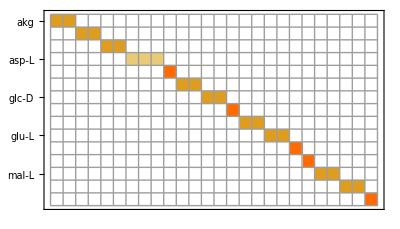

```mathematica
MatrixPlot[emuMixing,
FrameTicks->{Transpose[{Range[Length[measuredMetNames]],measuredMetNames}],None},Mesh->True]
```

MIDs to fit
Select MID data by metabolite and sample group

```mathematica
midsToFit=Block[{mapIndex,metIndex},
mapIndex=ReindexList[measuredMetNames,measuredMap⟦All,3⟧];
metIndex=ReindexList[measuredMap⟦mapIndex,1⟧,measuredMetIds];
Table[
Normal/@MIDNormalize/@measuredMIDs⟦metIndex⟦i⟧,measuredMap⟦mapIndex⟦i⟧,2⟧⟧,
{i,Length[measuredMetNames]}]];
```

## Uptake/release data

### Map uptake/release measurements to EMU fluxes (flux mixing matrix)

This map defines the measured reactions (linear combinations)

```mathematica
fluxMeasurementMap={
{"ala-L","ala-L_IN",-1},{"ala-L","ala-L_OUT",1},
{"arg-L","arg-L_IN",-1},{"arg-L","arg-L_OUT",1},
{"asp-L","asp-L_IN",-1},{"asp-L","asp-L_OUT",1},
{"gln-L","gln-L_IN",-1},
{"gly","gly_IN",-1},
{"ser-L","ser-L_IN",-1},{"ser-L","ser-L_OUT",1},
{"lac-L","lac-L_OUT",1},
{"glc-D","GLCtout_f",1},{"glc-D","GLCtin_f",-1},
{"glc-D_tot","glc-D_IN",1},
{"urea","urea_OUT",1},
{ "protdeg_ala","PROTDEG_ALA_f",1},
{ "protdeg_arg","PROTDEG_ARG_f",1},
{ "protdeg_asp","PROTDEG_ASP_f",1},
{ "protdeg_glu","PROTDEG_GLU_f",1},
{ "protsyn_ala","PROTSYN_ALA_f",1},
{ "protsyn_arg","PROTSYN_ARG_f",1},
{ "protsyn_asp","PROTSYN_ASP_f",1},
{ "protsyn_glu","PROTSYN_GLU_f",1},
{"cellwork","CELLWORK_f",1},
{"glycogen","GLYCOGEN_BREAK_f",1},
{"nadph_demand","NADPH_REDOX_f",1}
};
```

Ensure measurement names do not collide with flux names

```mathematica
fluxMeasurementMap⟦All,1⟧=Table[StringJoin["meas_",s],{s,fluxMeasurementMap⟦All,1⟧}];
```

```mathematica
measuredBoundaryIds=Union[fluxMeasurementMap⟦All,1⟧]
```

{meas_ala-L,meas_arg-L,meas_asp-L,meas_cellwork,meas_glc-D,meas_glc-D_tot,meas_gln-L,meas_gly,meas_glycogen,meas_lac-L,meas_nadph_demand,meas_protdeg_ala,meas_protdeg_arg,meas_protdeg_asp,meas_protdeg_glu,meas_protsyn_ala,meas_protsyn_arg,meas_protsyn_asp,meas_protsyn_glu,meas_ser-L,meas_urea}

```mathematica
measReactions=Union[fluxMeasurementMap⟦All,2⟧]
```

{ala-L_IN,ala-L_OUT,arg-L_IN,arg-L_OUT,asp-L_IN,asp-L_OUT,CELLWORK_f,glc-D_IN,GLCtin_f,GLCtout_f,gln-L_IN,GLYCOGEN_BREAK_f,gly_IN,lac-L_OUT,NADPH_REDOX_f,PROTDEG_ALA_f,PROTDEG_ARG_f,PROTDEG_ASP_f,PROTDEG_GLU_f,PROTSYN_ALA_f,PROTSYN_ARG_f,PROTSYN_ASP_f,PROTSYN_GLU_f,ser-L_IN,ser-L_OUT,urea_OUT}

```mathematica
fluxMixing=SparseArray[
Thread[Rule[
Transpose[{
ReindexList[fluxMeasurementMap⟦All,1⟧,measuredBoundaryIds],
ReindexList[fluxMeasurementMap⟦All,2⟧,measReactions]}],
fluxMeasurementMap⟦All,3⟧]],
{Length[measuredBoundaryIds],Length[measReactions]}]
```

SparseArray[<26>, {21, 26}]

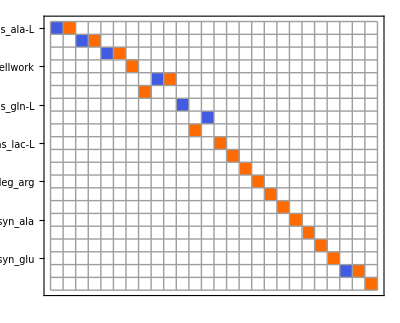

```mathematica
MatrixPlot[fluxMixing,
FrameTicks->{Transpose[{Range[Length[measuredBoundaryIds]],measuredBoundaryIds}],None},Mesh->True]
```

### Import uptake/release data

```mathematica
uptakeRelease=First[Import[
"C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\medium-concentrations\\uptake-release-fluxes-all.xlsx"]];
```

```mathematica
uptakeReleaseExpName="L016";
```

Preferred data source types

```mathematica
uptakeReleasePrecedence={"clin chem","12C int std","elisa","peak ratio","imputed","literature","total"};
uptakeReleasePrecedence=Thread[Rule[uptakeReleasePrecedence,Range[Length[uptakeReleasePrecedence]]]]
```

{clin chem→1,12C int std→2,elisa→3,peak ratio→4,imputed→5,literature→6,total→7}

```mathematica
{boundaryFluxMean,boundaryFluxSD}=Block[{cols,ur},
cols=Join[{1,2},Position[uptakeRelease⟦1⟧,uptakeReleaseExpName]⟦1,1⟧+{0,1}];
ur=Cases[Drop[uptakeRelease⟦All,cols⟧,2],{_,_,Except[""],_}];
ur⟦All,1⟧=Table[StringJoin["meas_",s],{s,ur⟦All,1⟧}];
(* sort by precedence *)
ur=SortBy[ur,Replace[#⟦2⟧,uptakeReleasePrecedence]&];
Transpose[
Replace[measuredBoundaryIds,
Thread[Rule[ur⟦All,1⟧,ur⟦All,{3,4}⟧]],{1}]]]
```

{{-11.0685,-8.29496,-1.93634,6500.,75.339,619.048,-16.1411,-2.45657,310.,140.558,300.,36.58,12.98,23.6,24.19,36.58,12.98,23.6,24.19,-2.2805,100.},{7.44441,1.4535,1.26735,1950.,7.5339,61.9048,12.3192,6.8255,100.,14.0558,150.,10.974,3.894,7.08,7.257,10.974,3.894,7.08,7.257,2.45732,50.}}

```mathematica
TableForm[Transpose[{boundaryFluxMean,boundaryFluxSD}],TableHeadings->{measuredBoundaryIds,None}]
```

meas_ala-L | -11.0685 | 7.44441
meas_arg-L | -8.29496 | 1.4535
meas_asp-L | -1.93634 | 1.26735
meas_cellwork | 6500. | 1950.
meas_glc-D | 75.339 | 7.5339
meas_glc-D_tot | 619.048 | 61.9048
meas_gln-L | -16.1411 | 12.3192
meas_gly | -2.45657 | 6.8255
meas_glycogen | 310. | 100.
meas_lac-L | 140.558 | 14.0558
meas_nadph_demand | 300. | 150.
meas_protdeg_ala | 36.58 | 10.974
meas_protdeg_arg | 12.98 | 3.894
meas_protdeg_asp | 23.6 | 7.08
meas_protdeg_glu | 24.19 | 7.257
meas_protsyn_ala | 36.58 | 10.974
meas_protsyn_arg | 12.98 | 3.894
meas_protsyn_asp | 23.6 | 7.08
meas_protsyn_glu | 24.19 | 7.257
meas_ser-L | -2.2805 | 2.45732
meas_urea | 100. | 50.

## Characterize the flux space

### Min/max fluxes

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{97,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

70

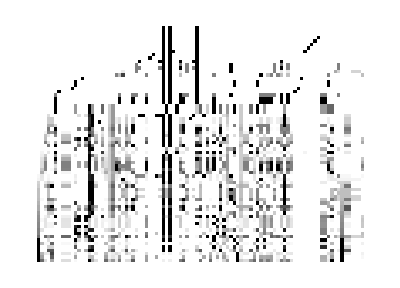

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Mina / max fluxes per reaction

```mathematica
TableForm[
Map[{Min[#],Max[#]}&,Transpose[NetFlux/@fluxMinMax]],
TableHeadings->{ReactionID/@Reactions[net],{"min","max"}}]
```

| min | max
2AMACHYD | 0 | 1000.
ACONTm | 0 | 583.333
ADK1 | 0 | 593.915
AKGDm | 0 | 666.667
AKGtm | -1000. | 1000.
ALATA_L | -1000. | 1000.
ALAtl | 0 | 1000.
ARGN | 0 | 593.915
ARGSL | 0 | 593.915
ARGSS | 0 | 593.915
ARGtl | 0 | 1000.
ASPTA | -1000. | 1000.
ASPTAm | 0 | 1000.
ASPtl | 0 | 1000.
ASPtm | 0 | 1000.
ATPS4m | 0 | 1000.
ATPtm | 0 | 1000.
CBPSam | 0 | 593.915
CELLWORK | 0 | 1000.
CO2tm | -736.842 | 870.968
CSm | 0 | 583.333
CYOOm | 0 | 333.333
CYOR-u10m | 0 | 666.667
ENO | -1000. | 1000.
FBA | -333.333 | 1000.
FBP | 0 | 1000.
FUMm | 0 | 1000.
FUMtm | 0 | 593.915
G3PD1 | 0 | 1000.
G6PDH2r | 0 | 500.
G6PPer | 0 | 1000.
G6Pter | -1000. | 1000.
GAPD | -500. | 1000.
GHMT2r | -1000. | 1000.
GLCmix | 0 | 1000.
GLCtin | 0 | 1000.
GLCtout | 0 | 1000.
GLNtm | 0 | 1000.
GLUDxm | -1000. | 1000.
GLUNm | 0 | 1000.
GLUtl | 0 | 1000.
GLUt2m | -1000. | 1000.
GLYCOGEN_BREAK | 0 | 1000.
GLYCPH | 0 | 1000.
GND | 0 | 500.
GTHS | 0 | 1000.
H2Oter | 0 | 1000.
H2Otm | -1000. | 1000.
HCO3Em | 0 | 1000.
HEX1 | 0 | 1000.
Htm2 | -1000. | 1000.
ICDHxm | 0 | 583.333
LDH_L | 0 | 1000.
MALtm | -1000. | 1000.
MDH | -1000. | 1000.
MDHm | -904.762 | 1000.
NADH2-u10m | 0 | 400.
NADPH_REDOX | 0 | 1000.
NDPK1 | 0 | 1000.
NH4tm | -1000. | 1000.
O2tm | 0 | 333.333
OCBTm | 0 | 593.915
ORNt4m | 0 | 593.915
PCm | 0 | 1000.
PDHm | 0 | 583.333
PEPCK | 0 | 1000.
PFK | 0 | 1000.
PGCD | 0 | 1000.
PGI | -666.667 | 1000.
PGK | -500. | 1000.
PGL | 0 | 500.
PGM | -1000. | 1000.
PGMTer | 0 | 1000.
PIt2m | 0 | 1000.
PIter | -1000. | 1000.
PPA | 0 | 593.915
PROTDEG_ALA | 0 | 1000.
PROTDEG_ARG | 0 | 1000.
PROTDEG_ASP | 0 | 1000.
PROTDEG_GLU | 0 | 1000.
PROTSYN_ALA | 0 | 1000.
PROTSYN_ARG | 0 | 1000.
PROTSYN_ASP | 0 | 1000.
PROTSYN_GLU | 0 | 1000.
PSERT | 0 | 1000.
PSP_L | 0 | 1000.
PYK | 0 | 1000.
PYRt2m | 0 | 1000.
RPE | 0 | 333.333
RPI | 0 | 500.
SERHL | 0 | 1000.
SUCD1m | 0 | 666.667
SUCOASm | 0 | 666.667
TALA | 0 | 166.667
TKT1 | 0 | 166.667
TKT2 | 0 | 166.667
TPI | -700. | 500.

Specific flux vector

Generating random flux states from the min/max vectors, scaled to output = 100

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

### Check for blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

{}

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]//TableForm
```

<Reaction ACONTm(rev)> | cit_m <=> icit_m
<Reaction AKGDm(rev)> | akg_m + coa_m + nad_m <=> co2_m + nadh_m + succoa_m
<Reaction ASPTAm(rev)> | glu-L_m + oaa_m <=> akg_m + asp-L_m
<Reaction ATPtm(rev)> | adp_c + atp_m <=> adp_m + atp_c
<Reaction GLUNm(rev)> | gln-L_m + h2o_m <=> glu-L_m + nh4_m
<Reaction H2Oter(rev)> | h2o_c <=> h2o_r
<Reaction ICDHxm(rev)> | icit_m + nad_m <=> akg_m + co2_m + nadh_m
<Reaction LDH_L(rev)> | h_c + nadh_c + pyr_c <=> lac-L_c + nad_c
<Reaction PYRt2m(rev)> | pyr_c <=> pyr_m

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[h2o,Output,Boundary]}

### Free fluxes

This is setup to select boundary fluxes first, then internal fluxes (typically controlling type II pathways)

```mathematica
freeFluxIndex=FindFreeFluxes[net]
```

{{75,88,91},{6,9,10,11,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}}

```mathematica
Reactions[net]⟦freeFluxIndex⟦1⟧⟧
```

{<Reaction PIter(rev)>,<Reaction PYRt2m(rev)>,<Reaction SERHL>}

```mathematica
BoundaryFluxNames[bnet]⟦freeFluxIndex⟦2⟧⟧
```

{gln-L_IN,glycogen_IN,h2o_IN,h_IN,o2_IN,prot_ala_IN,prot_arg_IN,prot_asp_IN,prot_glu_IN,ser-L_IN,thf_IN,ala-L_OUT,arg-L_OUT,asp-L_OUT,co2_OUT,energy_OUT,glc-D_OUT,glu-L_OUT,gly_OUT,glyc_OUT,gthrd_OUT,h2o_OUT,h_OUT,lac-L_OUT,mlthf_OUT,nh4_OUT,prot_ala_OUT,prot_arg_OUT,prot_asp_OUT,prot_glu_OUT,r5p_OUT,ser-L_OUT,thf_OUT,urea_OUT}

Total # free variables

```mathematica
Length[Flatten[freeFluxIndex]]
```

37

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMaps,bmaps,{"C"},targets,symmetry];
Length[emuReactions]
```

1065

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[123,<akg_m{(123)}>,<glu-L_m{(123)}>,1],EMUReaction[22,<cit_m{(126)}>,<icit_m{(124)}>,1],EMUReaction[105,<glu-L_c{(1)}>,<akg_c{(1)}>,1],EMUReaction[109,<ru5p-D_c{(13)}>,<xu5p-D_c{(13)}>,1],EMUReaction[139,<mal-L_m{(3)}>,<mal-L_c{(3)}>,1],EMUReaction[59,<glu-L_m{(4)}>,<akg_m{(4)}>,1],EMUReaction[91,<6pgl_c{(3)}>,<6pgc_c{(3)}>,1],EMUReaction[97,<prot_ala_l{(3)}>,<ala-L_l{(3)}>,1],EMUReaction[46,<fdp_c{(13)}>,<f6p_c{(13)}>,1],EMUReaction[6,<gln-L_i{(2)}>,<gln-L_c{(2)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

550

```mathematica
SortBy[
Cases[emuReactions,
EMUReaction[i_,s_EMU,p:EMU[Metabolite["glc-D",__],_],_]:>{emuReactionNames⟦i⟧,s,p}],Last]//TableForm
```

GLCtin_f | <glc-D_v{(1)}> | <glc-D_c{(1)}>
GLCtin_f | <glc-D_v{(2)}> | <glc-D_c{(2)}>
GLCtin_f | <glc-D_v{(3)}> | <glc-D_c{(3)}>
GLCtin_f | <glc-D_v{(4)}> | <glc-D_c{(4)}>
GLCtin_f | <glc-D_v{(5)}> | <glc-D_c{(5)}>
GLCtin_f | <glc-D_v{(6)}> | <glc-D_c{(6)}>
GLCtin_f | <glc-D_v{(12)}> | <glc-D_c{(12)}>
GLCtin_f | <glc-D_v{(23)}> | <glc-D_c{(23)}>
GLCtin_f | <glc-D_v{(45)}> | <glc-D_c{(45)}>
GLCtin_f | <glc-D_v{(56)}> | <glc-D_c{(56)}>
GLCtin_f | <glc-D_v{(123)}> | <glc-D_c{(123)}>
GLCtin_f | <glc-D_v{(456)}> | <glc-D_c{(456)}>
GLCtin_f | <glc-D_v{(1234)}> | <glc-D_c{(1234)}>
GLCtin_f | <glc-D_v{(123456)}> | <glc-D_c{(123456)}>
G6PPer_f | <g6p_r{(123456)}> | <glc-D_r{(123456)}>
GLCmix_f | <glc-D_v{(123456)}> | <glc-D_e{(123456)}>
GLCtout_f | <glc-D_r{(123456)}> | <glc-D_e{(123456)}>
glc-D_IN | <glc-D_i{(1)}> | <glc-D_v{(1)}>
glc-D_IN | <glc-D_i{(2)}> | <glc-D_v{(2)}>
glc-D_IN | <glc-D_i{(3)}> | <glc-D_v{(3)}>
glc-D_IN | <glc-D_i{(4)}> | <glc-D_v{(4)}>
glc-D_IN | <glc-D_i{(5)}> | <glc-D_v{(5)}>
glc-D_IN | <glc-D_i{(6)}> | <glc-D_v{(6)}>
glc-D_IN | <glc-D_i{(12)}> | <glc-D_v{(12)}>
glc-D_IN | <glc-D_i{(23)}> | <glc-D_v{(23)}>
glc-D_IN | <glc-D_i{(45)}> | <glc-D_v{(45)}>
glc-D_IN | <glc-D_i{(56)}> | <glc-D_v{(56)}>
glc-D_IN | <glc-D_i{(123)}> | <glc-D_v{(123)}>
glc-D_IN | <glc-D_i{(456)}> | <glc-D_v{(456)}>
glc-D_IN | <glc-D_i{(1234)}> | <glc-D_v{(1234)}>
glc-D_IN | <glc-D_i{(123456)}> | <glc-D_v{(123456)}>

Ensure targets are contained in EMUs

```mathematica
Complement[targets,emus]
```

{}

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 241 internals, 43 substrates, 0 condensations >
2 | <EMUEquation (2), 152 internals, 27 substrates, 5 condensations >
3 | <EMUEquation (3), 84 internals, 15 substrates, 5 condensations >
4 | <EMUEquation (4), 37 internals, 6 substrates, 4 condensations >
5 | <EMUEquation (5), 18 internals, 4 substrates, 2 condensations >
6 | <EMUEquation (6), 18 internals, 4 substrates, 6 condensations >

## Substrates

### Specify input isotopomers (tracers)

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

### Check: simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

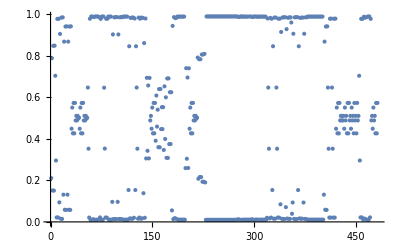
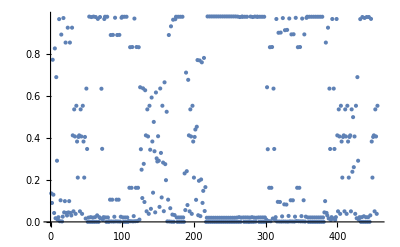
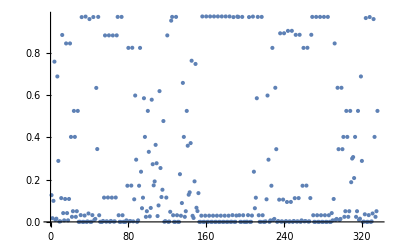
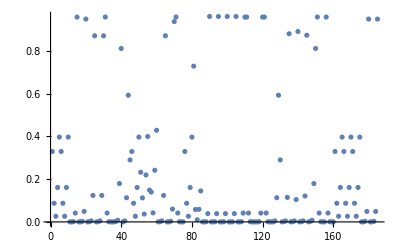
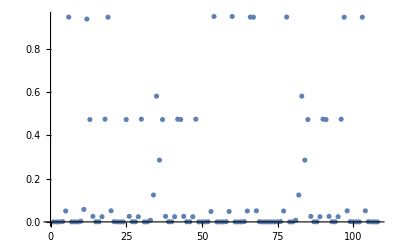
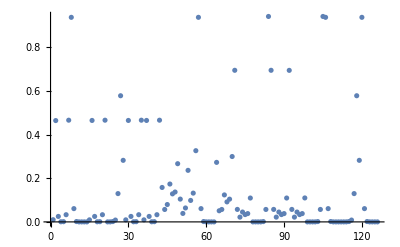

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## Analyze fluxes with GAMS, standard method

### Parameters

```mathematica
gamsModelName="liver-model";
```

```mathematica
gamsDir=FileNameJoin[{Directory[],patientId,"gams"}]
```

C:\code\liver-flux-analysis\flux-analysis-liver\L016\gams

```mathematica
If[!DirectoryQ[gamsDir],CreateDirectory[gamsDir]]
```

Here “experiments” referes to tracer settings (only one)

```mathematica
experiments={"experiment1"};
```

Smallest standard deviation allowed

```mathematica
minSD=0.03;
```

### Generate optimization model

Export model file

```mathematica
initFlux=RandomFluxState[10];
```

```mathematica
fluxCIReactions=Reactions[net];
```

```mathematica
fluxCIReactions=Cases[Reactions[net],Reaction["GAPD"|"GLYCOGEN_BREAK",__]]
```

{<Reaction GAPD(rev)>,<Reaction GLYCOGEN_BREAK>}

```mathematica
fluxCIReactions={}
```

{}

```mathematica
GAMSExport[gamsDir,gamsModelName,
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes -- here we need to give a meas x reaction matrix *)
measuredBoundaryIds,measReactions,boundaryFluxMean,boundaryFluxSD,fluxMixing,
(* measured MIDs *)
experiments,measuredMetNames,{Mean/@midsToFit},{Map[Max[StandardDeviation[#],minSD]&,midsToFit]},
(* targets *)
targets,emuMixing,
initFlux,"FluxCI"->fluxCIReactions]
```

C:\code\liver-flux-analysis\flux-analysis-liver\L016\gams\liver-model.gms

### Run GAMS

From command line ...

## Import GAMS solutions

### Estimated mixing matrix

```mathematica
emuMixingGams=ImportGAMSEmuMixing[gamsDir,gamsModelName,measuredMetNames,targets]
```

SparseArray[<21>, {15, 26}]

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixingGams];
Transpose[{measuredMetNames⟦ij⟦All,1⟧⟧,targets⟦ij⟦All,2⟧⟧,NonZeroElements[emuMixingGams]}]]//TableForm
```

akg | <akg_c{(12345)}> | 1.
ala-L | <ala-L_c{(123)}> | 1.
arg-L | <arg-L_c{(123456)}> | 0.446971
arg-L | <arg-L_l{(123456)}> | 0.553029
asp-L | <asp-L_c{(1234)}> | 0.264715
asp-L | <asp-L_l{(1234)}> | 0.206839
asp-L | <asp-L_m{(1234)}> | 0.528446
cit | <cit_m{(123456)}> | 1.
citr-L | <citr-L_c{(123456)}> | 0.5
citr-L | <citr-L_m{(123456)}> | 0.5
glc-D | <glc-D_c{(123456)}> | 0.492995
glc-D | <glc-D_r{(123456)}> | 0.507005
glc-D_EC | <glc-D_e{(123456)}> | 1.
gln-L | <gln-L_m{(12345)}> | 1.
glu-L | <glu-L_m{(12345)}> | 1.
gly | <gly_c{(12)}> | 1.
glyc3p | <glyc3p_c{(123)}> | 1.
mal-L | <mal-L_m{(1234)}> | 1.
orn | <orn_c{(12345)}> | 0.5
orn | <orn_m{(12345)}> | 0.5
ser-L | <ser-L_c{(123)}> | 1.

### Fitted MIDs

Import results

```mathematica
midGams=ImportGAMSIsotopes[gamsDir,gamsModelName,experiments,emus];
```

Check dimensions

```mathematica
Length/@midGams⟦1⟧==(EMUSize/@emus)+1
```

True

Recover fitted MIDs as mixing x target MIDs

```mathematica
fittedMIDs=Block[{ix,mix,mid},
mix=emuMixingGams;
mid=midGams⟦1,ReindexList[targets,emus]⟧;
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.mid⟦ix⟧,
{em,mix}]];
```

```mathematica
TableForm[fittedMIDs,TableHeadings->{measuredMetNames,None}]
```

akg | 0.688126 | 0.0958194 | 0.0779105 | 0.0373245 | 0.0221809 | 0.0786385 | 
ala-L | 0.462369 | 0.0686399 | 0.15395 | 0.315041 |  |  | 
arg-L | 0.781484 | 0.0508664 | 0.00138006 | 0.000074242 | 0.0027415 | 0.0574896 | 0.105964
asp-L | 0.601747 | 0.110324 | 0.112758 | 0.115187 | 0.0599841 |  | 
cit | 0.429987 | 0.157073 | 0.171358 | 0.0838694 | 0.0464876 | 0.109838 | 0.00138833
citr-L | 0.587763 | 0.0391853 | 0.00109134 | 0.000372552 | 0.0176471 | 0.349543 | 0.00439788
glc-D | 0.475313 | 0.0308451 | 0.000834104 | 0.0000215946 | 0.000710452 | 0.02813 | 0.464146
glc-D_EC | 0.187063 | 0.0121393 | 0.000328357 | 0.0000202673 | 0.00115342 | 0.045674 | 0.753622
gln-L | 0.314952 | 0.111022 | 0.124029 | 0.0600708 | 0.0465455 | 0.343381 | 
glu-L | 0.408212 | 0.143897 | 0.160751 | 0.077571 | 0.0461059 | 0.163462 | 
gly | 0.582174 | 0.0464784 | 0.371348 |  |  |  | 
glyc3p | 0.642803 | 0.0996014 | 0.0843307 | 0.173264 |  |  | 
mal-L | 0.495272 | 0.143743 | 0.149247 | 0.145662 | 0.0660769 |  | 
orn | 0.595163 | 0.0321856 | 0.000699867 | 0.000368431 | 0.0178646 | 0.353719 | 
ser-L | 0.509876 | 0.112588 | 0.318602 | 0.058934 |  |  |

Compare fitted MIDs (gray) with measured (black)

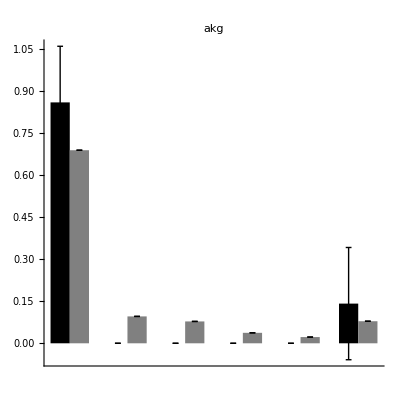
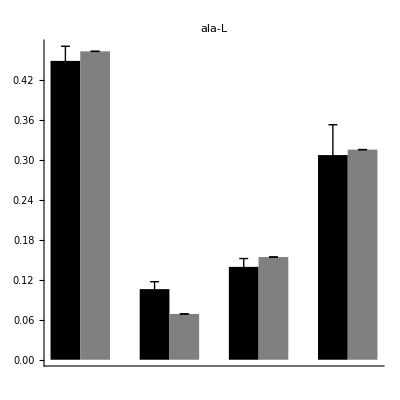
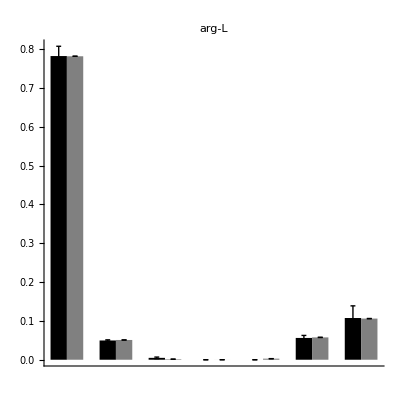
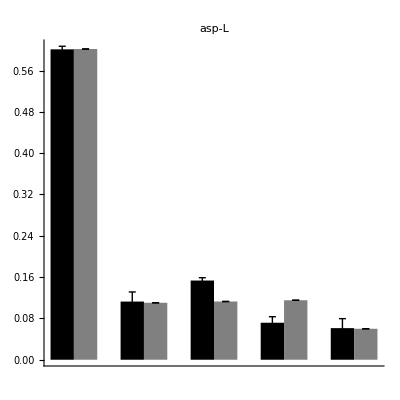
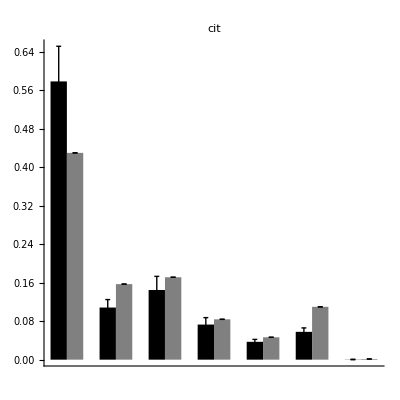
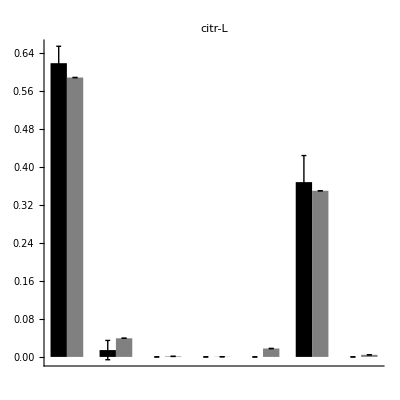
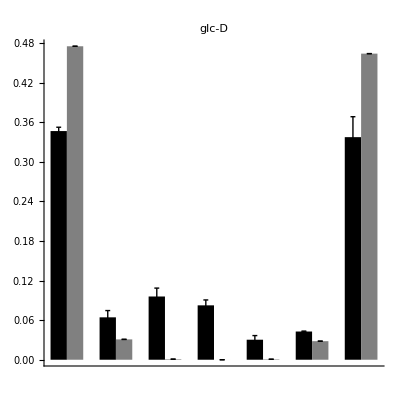
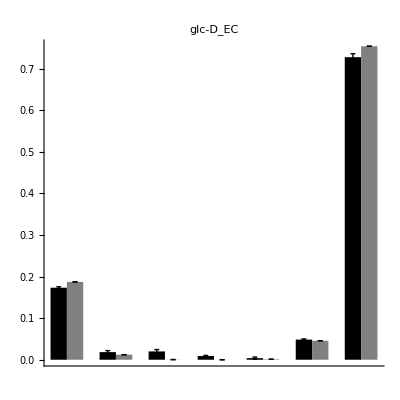

```mathematica
Table[
ErrorBarChart[
Transpose/@{midsToFit⟦i⟧,Table[fittedMIDs⟦i⟧,{3}]},
AspectRatio->1,PlotLabel->measuredMetNames⟦i⟧],
{i,Length[measuredMetNames]}]
```

Scatter plot of all fitted MIDs

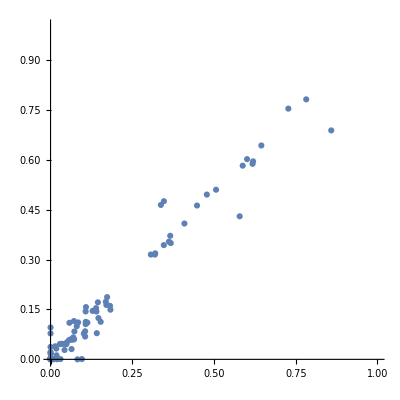

```mathematica
ListPlot[
Transpose[{Flatten[Mean/@midsToFit],Flatten[fittedMIDs]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

### Fluxes at optimum

Import

```mathematica
fluxGams=ImportGAMSFluxes[gamsDir,gamsModelName,net,EMUFluxMap[net]]
```

<FluxState, 97 reactions, 43 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 152.655 | 0. | 152.655
<Reaction ACONTm(rev)> | 100000. | 99954.8 | 45.2496
<Reaction ADK1> | 8.82925 | 0. | 8.82925
<Reaction AKGDm(rev)> | 65.0765 | 0.001 | 65.0755
<Reaction AKGtm(rev)> | 40.5931 | 0.001 | 40.5921
<Reaction ALATA_L(rev)> | 364.126 | 353.079 | 11.0471
<Reaction ALAtl> | 35.396 | 0. | 35.396
<Reaction ARGN> | 8.82925 | 0. | 8.82925
<Reaction ARGSL> | 8.82925 | 0. | 8.82925
<Reaction ARGSS> | 8.82925 | 0. | 8.82925
<Reaction ARGtl> | 11.4069 | 0. | 11.4069
<Reaction ASPTA(rev)> | 100000. | 99903.9 | 96.0971
<Reaction ASPTAm(rev)> | 102.963 | 0.001 | 102.962
<Reaction ASPtl> | 23.0694 | 0. | 23.0694
<Reaction ASPtm> | 102.962 | 0. | 102.962
<Reaction ATPS4m> | 361.991 | 0. | 361.991
<Reaction ATPtm(rev)> | 335.102 | 0.001 | 335.101
<Reaction CBPSam> | 8.82925 | 0. | 8.82925
<Reaction CELLWORK> | 273.501 | 0. | 273.501
<Reaction CO2tm(rev)> | 99927.6 | 100000. | -72.4384
<Reaction CSm> | 45.2496 | 0. | 45.2496
<Reaction CYOOm> | 85.4133 | 0. | 85.4133
<Reaction CYOR-u10m> | 170.827 | 0. | 170.827
<Reaction ENO(rev)> | 0.001 | 0.001 | 0.
<Reaction FBA(rev)> | 132.136 | 0.001 | 132.135
<Reaction FBP> | 0.001 | 0. | 0.001
<Reaction FUMm> | 73.9048 | 0. | 73.9048
<Reaction FUMtm> | 8.82925 | 0. | 8.82925
<Reaction G3PD1> | 155.23 | 0. | 155.23
<Reaction G6PDH2r> | 176.656 | 0. | 176.656
<Reaction G6PPer> | 135.775 | 0. | 135.775
<Reaction G6Pter(rev)> | 0.001 | 171.856 | -171.855
<Reaction GAPD(rev)> | 48123.8 | 47976.1 | 147.736
<Reaction GHMT2r(rev)> | 4808.65 | 4811.26 | -2.6101
<Reaction GLCmix> | 544.679 | 0. | 544.679
<Reaction GLCtin> | 59.5411 | 0. | 59.5411
<Reaction GLCtout> | 135.775 | 0. | 135.775
<Reaction GLNtm> | 8.29076 | 0. | 8.29076
<Reaction GLUDxm(rev)> | 0.001 | 123.729 | -123.728
<Reaction GLUNm(rev)> | 36.2898 | 27.9991 | 8.29076
<Reaction GLUtl> | 31.344 | 0. | 31.344
<Reaction GLUt2m(rev)> | 0.001 | 29.0579 | -29.0569
<Reaction GLYCOGEN_BREAK> | 307.63 | 0. | 307.63
<Reaction GLYCPH> | 155.23 | 0. | 155.23
<Reaction GND> | 176.656 | 0. | 176.656
<Reaction GTHS> | 0.001 | 0. | 0.001
<Reaction H2Oter(rev)> | 135.776 | 0.001 | 135.775
<Reaction H2Otm(rev)> | 1.38702 | 447.351 | -445.964
<Reaction HCO3Em> | 83.1364 | 0. | 83.1364
<Reaction HEX1> | 59.5411 | 0. | 59.5411
<Reaction Htm2(rev)> | 0.001 | 288.386 | -288.385
<Reaction ICDHxm(rev)> | 100000. | 99954.8 | 45.2496
<Reaction LDH_L(rev)> | 140.244 | 0.001 | 140.243
<Reaction MALtm(rev)> | 0.001 | 0.00153305 | -0.000533046
<Reaction MDH(rev)> | 0.00153305 | 0.001 | 0.000533046
<Reaction MDHm(rev)> | 517.118 | 443.213 | 73.9042
<Reaction NADH2-u10m> | 105.751 | 0. | 105.751
<Reaction NADPH_REDOX> | 353.313 | 0. | 353.313
<Reaction NDPK1> | 96.0976 | 0. | 96.0976
<Reaction NH4tm(rev)> | 124.624 | 0.357918 | 124.266
<Reaction O2tm> | 85.4133 | 0. | 85.4133
<Reaction OCBTm> | 8.82925 | 0. | 8.82925
<Reaction ORNt4m> | 8.82925 | 0. | 8.82925
<Reaction PCm> | 74.3071 | 0. | 74.3071
<Reaction PDHm> | 45.2496 | 0. | 45.2496
<Reaction PEPCK> | 96.0976 | 0. | 96.0976
<Reaction PFK> | 132.136 | 0. | 132.136
<Reaction PGCD> | 147.736 | 0. | 147.736
<Reaction PGI(rev)> | 54.7412 | 0.001 | 54.7402
<Reaction PGK(rev)> | 26629.2 | 26481.4 | 147.736
<Reaction PGL> | 176.656 | 0. | 176.656
<Reaction PGM(rev)> | 0.001 | 0.001 | 0.
<Reaction PGMTer> | 307.63 | 0. | 307.63
<Reaction PIt2m> | 335.101 | 0. | 335.101
<Reaction PIter(rev)> | 172.942 | 1.08648 | 171.855
<Reaction PPA> | 8.82925 | 0. | 8.82925
<Reaction PROTDEG_ALA> | 35.396 | 0. | 35.396
<Reaction PROTDEG_ARG> | 11.4069 | 0. | 11.4069
<Reaction PROTDEG_ASP> | 23.0694 | 0. | 23.0694
<Reaction PROTDEG_GLU> | 31.344 | 0. | 31.344
<Reaction PROTSYN_ALA> | 35.7838 | 0. | 35.7838
<Reaction PROTSYN_ARG> | 18.1613 | 0. | 18.1613
<Reaction PROTSYN_ASP> | 23.0585 | 0. | 23.0585
<Reaction PROTSYN_GLU> | 19.8079 | 0. | 19.8079
<Reaction PSERT> | 147.736 | 0. | 147.736
<Reaction PSP_L> | 147.736 | 0. | 147.736
<Reaction PYK> | 96.0976 | 0. | 96.0976
<Reaction PYRt2m(rev)> | 119.558 | 0.001 | 119.557
<Reaction RPE> | 77.3944 | 0. | 77.3944
<Reaction RPI> | 99.2619 | 0. | 99.2619
<Reaction SERHL> | 152.655 | 0. | 152.655
<Reaction SUCD1m> | 65.0755 | 0. | 65.0755
<Reaction SUCOASm> | 65.0755 | 0. | 65.0755
<Reaction TALA> | 38.6972 | 0. | 38.6972
<Reaction TKT1> | 38.6972 | 0. | 38.6972
<Reaction TKT2> | 38.6972 | 0. | 38.6972
<Reaction TPI(rev)> | 44.5222 | 67.6178 | -23.0956

Boundary fluxes

```mathematica
TableForm[
BoundaryFlux[fluxGams],
TableHeadings->{BoundaryFluxNames[bnet],None}]
```

ala-L_IN | 59.9402
arg-L_IN | 6.75542
asp-L_IN | 9.34485
co2_IN | 99654.8
glc-D_IN | 604.22
gln-L_IN | 8.29076
glucys_IN | 0.001
gly_IN | 2.6121
glycogen_IN | 307.63
h2o_IN | 463.205
h_IN | 1.00333
mlthf_IN | 371.832
o2_IN | 85.4133
pi_IN | 60.5647
prot_ala_IN | 35.396
prot_arg_IN | 11.4069
prot_asp_IN | 23.0694
prot_glu_IN | 31.344
ser-L_IN | 30.0178
thf_IN | 2.18732
ala-L_OUT | 48.5053
arg-L_OUT | 0.001
asp-L_OUT | 7.39116
co2_OUT | 100000.
energy_OUT | 273.501
glc-D_OUT | 680.454
glu-L_OUT | 0.001
gly_OUT | 0.001
glyc_OUT | 155.23
gthrd_OUT | 0.001
h2o_OUT | 0.001
h_OUT | 805.983
lac-L_OUT | 140.243
mlthf_OUT | 369.222
nh4_OUT | 28.3885
prot_ala_OUT | 35.7838
prot_arg_OUT | 18.1613
prot_asp_OUT | 23.0585
prot_glu_OUT | 19.8079
r5p_OUT | 60.5647
ser-L_OUT | 27.7093
thf_OUT | 4.79742
urea_OUT | 8.82925

#### Fitted flux measurements.

```mathematica
Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
v=Join[EMUFluxMap[net][fluxGams],BoundaryFlux[fluxGams]];
ix=ReindexList[measReactions,rl];
TableForm[
Transpose[{fluxMixing.v⟦ix⟧,boundaryFluxMean}],
TableHeadings->{measuredBoundaryIds,{"fitted","measured"}}]]
```

| fitted | measured
meas_ala-L | -11.4349 | -11.0685
meas_arg-L | -6.75442 | -8.29496
meas_asp-L | -1.95369 | -1.93634
meas_cellwork | 273.501 | 6500.
meas_glc-D | 76.2335 | 75.339
meas_glc-D_tot | 604.22 | 619.048
meas_gln-L | -8.29076 | -16.1411
meas_gly | -2.6121 | -2.45657
meas_glycogen | 307.63 | 310.
meas_lac-L | 140.243 | 140.558
meas_nadph_demand | 353.313 | 300.
meas_protdeg_ala | 35.396 | 36.58
meas_protdeg_arg | 11.4069 | 12.98
meas_protdeg_asp | 23.0694 | 23.6
meas_protdeg_glu | 31.344 | 24.19
meas_protsyn_ala | 35.7838 | 36.58
meas_protsyn_arg | 18.1613 | 12.98
meas_protsyn_asp | 23.0585 | 23.6
meas_protsyn_glu | 19.8079 | 24.19
meas_ser-L | -2.30858 | -2.2805
meas_urea | 8.82925 | 100.

```mathematica
Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
v=Join[EMUFluxMap[net][fluxGams],BoundaryFlux[fluxGams]];
ix=ReindexList[measReactions,rl];
TableForm[v⟦ix⟧,TableHeadings->{measReactions}]]
```

ala-L_IN | 59.9402
ala-L_OUT | 48.5053
arg-L_IN | 6.75542
arg-L_OUT | 0.001
asp-L_IN | 9.34485
asp-L_OUT | 7.39116
CELLWORK_f | 273.501
glc-D_IN | 604.22
GLCtin_f | 59.5411
GLCtout_f | 135.775
gln-L_IN | 8.29076
GLYCOGEN_BREAK_f | 307.63
gly_IN | 2.6121
lac-L_OUT | 140.243
NADPH_REDOX_f | 353.313
PROTDEG_ALA_f | 35.396
PROTDEG_ARG_f | 11.4069
PROTDEG_ASP_f | 23.0694
PROTDEG_GLU_f | 31.344
PROTSYN_ALA_f | 35.7838
PROTSYN_ARG_f | 18.1613
PROTSYN_ASP_f | 23.0585
PROTSYN_GLU_f | 19.8079
ser-L_IN | 30.0178
ser-L_OUT | 27.7093
urea_OUT | 8.82925

#### Metabolite balances

```mathematica
Block[{rids,mids,v},
rids=ReactionID/@Reactions[net];
mids=MetaboliteShortName/@Metabolites[net];
v=NetFlux[fluxGams];
TableForm[
Table[
(part@(Stoichiometry[net]⟦i⟧*v)).rids,
{i,Length[mids]},{part,{PositivePart,NegativePart}}],
TableHeadings->{mids,None}]]
```

13dpg_c | 147.736 GAPD | 147.736 PGK
2amac_c | 152.655 SERHL | 152.655 2AMACHYD
2pg_c | 0 | 0
3pg_c | 147.736 PGK | 147.736 PGCD
3php_c | 147.736 PGCD | 147.736 PSERT
6pgc_c | 176.656 PGL | 176.656 GND
6pgl_c | 176.656 G6PDH2r | 176.656 PGL
accoa_m | 45.2496 PDHm | 45.2496 CSm
adp_c | 17.6585 ADK1+273.501 CELLWORK+0.001 GTHS+59.5411 HEX1+96.0976 NDPK1+132.136 PFK | 335.101 ATPtm+147.736 PGK+96.0976 PYK
adp_m | 335.101 ATPtm+17.6585 CBPSam+74.3071 PCm | 361.991 ATPS4m+65.0755 SUCOASm
akg_c | 147.736 PSERT | 40.5921 AKGtm+11.0471 ALATA_L+96.0971 ASPTA
akg_m | 40.5921 AKGtm+102.962 ASPTAm+45.2496 ICDHxm | 65.0755 AKGDm+123.728 GLUDxm
ala-L_c | 35.396 ALAtl | 11.0471 ALATA_L+35.7838 PROTSYN_ALA
ala-L_l | 35.396 PROTDEG_ALA | 35.396 ALAtl
amp_c | 8.82925 ARGSS | 8.82925 ADK1
arg-L_c | 8.82925 ARGSL+11.4069 ARGtl | 8.82925 ARGN+18.1613 PROTSYN_ARG
arg-L_l | 11.4069 PROTDEG_ARG | 11.4069 ARGtl
argsuc_c | 8.82925 ARGSS | 8.82925 ARGSL
asp-L_c | 23.0694 ASPtl+102.962 ASPtm | 8.82925 ARGSS+96.0971 ASPTA+23.0585 PROTSYN_ASP
asp-L_l | 23.0694 PROTDEG_ASP | 23.0694 ASPtl
asp-L_m | 102.962 ASPTAm | 102.962 ASPtm
atp_c | 335.101 ATPtm+147.736 PGK+96.0976 PYK | 8.82925 ADK1+8.82925 ARGSS+273.501 CELLWORK+0.001 GTHS+59.5411 HEX1+96.0976 NDPK1+132.136 PFK
atp_m | 361.991 ATPS4m+65.0755 SUCOASm | 335.101 ATPtm+17.6585 CBPSam+74.3071 PCm
cbp_m | 8.82925 CBPSam | 8.82925 OCBTm
cit_m | 45.2496 CSm | 45.2496 ACONTm
citr-L_c | 8.82925 ORNt4m | 8.82925 ARGSS
citr-L_m | 8.82925 OCBTm | 8.82925 ORNt4m
co2_c | 72.4384 CO2tm+176.656 GND+96.0976 PEPCK | 0
co2_m | 65.0755 AKGDm+45.2496 ICDHxm+45.2496 PDHm | 72.4384 CO2tm+83.1364 HCO3Em
coa_m | 45.2496 CSm+65.0755 SUCOASm | 65.0755 AKGDm+45.2496 PDHm
dhap_c | 132.135 FBA+23.0956 TPI | 155.23 G3PD1
e4p_c | 38.6972 TALA | 38.6972 TKT2
energy_c | 273.501 CELLWORK | 0
f6p_c | 0.001 FBP+54.7402 PGI+38.6972 TALA+38.6972 TKT2 | 132.136 PFK
fdp_c | 132.136 PFK | 132.135 FBA+0.001 FBP
ficytC_m | 341.653 CYOOm | 341.653 CYOR-u10m
focytC_m | 341.653 CYOR-u10m | 341.653 CYOOm
fum_c | 8.82925 ARGSL | 8.82925 FUMtm
fum_m | 8.82925 FUMtm+65.0755 SUCD1m | 73.9048 FUMm
g1p_r | 307.63 GLYCOGEN_BREAK | 307.63 PGMTer
g3p_c | 132.135 FBA+38.6972 TKT1+38.6972 TKT2 | 147.736 GAPD+38.6972 TALA+23.0956 TPI
g6p_c | 171.855 G6Pter+59.5411 HEX1 | 176.656 G6PDH2r+54.7402 PGI
g6p_r | 307.63 PGMTer | 135.775 G6PPer+171.855 G6Pter
gdp_c | 96.0976 PEPCK | 96.0976 NDPK1
glc-D_c | 59.5411 GLCtin | 59.5411 HEX1
glc-D_e | 544.679 GLCmix+135.775 GLCtout | 0
glc-D_r | 135.775 G6PPer | 135.775 GLCtout
glc-D_v | 0 | 544.679 GLCmix+59.5411 GLCtin
gln-L_c | 0 | 8.29076 GLNtm
gln-L_m | 8.29076 GLNtm | 8.29076 GLUNm
glucys_c | 0 | 0.001 GTHS
glu-L_c | 11.0471 ALATA_L+96.0971 ASPTA+29.0569 GLUt2m+31.344 GLUtl | 19.8079 PROTSYN_GLU+147.736 PSERT
glu-L_l | 31.344 PROTDEG_GLU | 31.344 GLUtl
glu-L_m | 123.728 GLUDxm+8.29076 GLUNm | 102.962 ASPTAm+29.0569 GLUt2m
gly_c | 0 | 2.6101 GHMT2r+0.001 GTHS
glyc3p_c | 155.23 G3PD1 | 155.23 GLYCPH
glyc_c | 155.23 GLYCPH | 0
glycogen_r | 0 | 307.63 GLYCOGEN_BREAK
gthrd_c | 0.001 GTHS | 0
gtp_c | 96.0976 NDPK1 | 96.0976 PEPCK
h2o_c | 445.964 H2Otm+152.655 SERHL | 152.655 2AMACHYD+8.82925 ARGN+273.501 CELLWORK+0.001 FBP+2.6101 GHMT2r+155.23 GLYCPH+135.775 H2Oter+176.656 PGL+8.82925 PPA+147.736 PSP_L
h2o_m | 361.991 ATPS4m+170.827 CYOOm+123.728 GLUDxm | 45.2496 CSm+73.9048 FUMm+8.29076 GLUNm+445.964 H2Otm+83.1364 HCO3Em
h2o_r | 135.775 H2Oter | 135.775 G6PPer
h_c | 8.82925 ARGSS+273.501 CELLWORK+176.656 G6PDH2r+147.736 GAPD+0.001 GTHS+59.5411 HEX1+0.000533046 MDH+353.313 NADPH_REDOX+132.136 PFK+147.736 PGCD+176.656 PGL+8.82925 PPA | 155.23 G3PD1+288.385 Htm2+140.243 LDH_L+96.0976 PYK
hco3_m | 83.1364 HCO3Em | 8.82925 CBPSam+74.3071 PCm
h_ims_m | 341.653 CYOOm+683.306 CYOR-u10m+423.004 NADH2-u10m | 1447.96 ATPS4m
h_m | 1085.97 ATPS4m+17.6585 CBPSam+45.2496 CSm+83.1364 HCO3Em+288.385 Htm2+73.9042 MDHm+8.82925 OCBTm+74.3071 PCm | 683.306 CYOOm+341.653 CYOR-u10m+123.728 GLUDxm+528.755 NADH2-u10m
icit_m | 45.2496 ACONTm | 45.2496 ICDHxm
lac-L_c | 140.243 LDH_L | 0
mal-L_c | 0.000533046 MALtm | 0.000533046 MDH
mal-L_m | 73.9048 FUMm | 0.000533046 MALtm+73.9042 MDHm
mlthf_c | 0 | 2.6101 GHMT2r
nad_c | 155.23 G3PD1+140.243 LDH_L | 147.736 GAPD+0.000533046 MDH+147.736 PGCD
nadh_c | 147.736 GAPD+0.000533046 MDH+147.736 PGCD | 155.23 G3PD1+140.243 LDH_L
nadh_m | 65.0755 AKGDm+45.2496 ICDHxm+73.9042 MDHm+45.2496 PDHm | 123.728 GLUDxm+105.751 NADH2-u10m
nad_m | 123.728 GLUDxm+105.751 NADH2-u10m | 65.0755 AKGDm+45.2496 ICDHxm+73.9042 MDHm+45.2496 PDHm
nadp_c | 353.313 NADPH_REDOX | 176.656 G6PDH2r+176.656 GND
nadph_c | 176.656 G6PDH2r+176.656 GND | 353.313 NADPH_REDOX
nh4_c | 152.655 2AMACHYD | 124.266 NH4tm
nh4_m | 8.29076 GLUNm+124.266 NH4tm | 8.82925 CBPSam+123.728 GLUDxm
o2_c | 0 | 85.4133 O2tm
o2_m | 85.4133 O2tm | 85.4133 CYOOm
oaa_c | 96.0971 ASPTA+0.000533046 MDH | 96.0976 PEPCK
oaa_m | 73.9042 MDHm+74.3071 PCm | 102.962 ASPTAm+45.2496 CSm
orn_c | 8.82925 ARGN | 8.82925 ORNt4m
orn_m | 8.82925 ORNt4m | 8.82925 OCBTm
pep_c | 96.0976 PEPCK | 96.0976 PYK
pi_c | 273.501 CELLWORK+0.001 FBP+155.23 GLYCPH+0.001 GTHS+17.6585 PPA+147.736 PSP_L | 147.736 GAPD+335.101 PIt2m+171.855 PIter
pi_m | 8.82925 CBPSam+8.82925 OCBTm+74.3071 PCm+335.101 PIt2m | 361.991 ATPS4m+65.0755 SUCOASm
pi_r | 135.775 G6PPer+171.855 PIter | 307.63 GLYCOGEN_BREAK
ppi_c | 8.82925 ARGSS | 8.82925 PPA
prot_ala_c | 35.7838 PROTSYN_ALA | 0
prot_ala_l | 0 | 35.396 PROTDEG_ALA
prot_arg_c | 18.1613 PROTSYN_ARG | 0
prot_arg_l | 0 | 11.4069 PROTDEG_ARG
prot_asp_c | 23.0585 PROTSYN_ASP | 0
prot_asp_l | 0 | 23.0694 PROTDEG_ASP
prot_glu_c | 19.8079 PROTSYN_GLU | 0
prot_glu_l | 0 | 31.344 PROTDEG_GLU
pser-L_c | 147.736 PSERT | 147.736 PSP_L
pyr_c | 152.655 2AMACHYD+11.0471 ALATA_L+96.0976 PYK | 140.243 LDH_L+119.557 PYRt2m
pyr_m | 119.557 PYRt2m | 74.3071 PCm+45.2496 PDHm
q10h2_m | 105.751 NADH2-u10m+65.0755 SUCD1m | 170.827 CYOR-u10m
q10_m | 170.827 CYOR-u10m | 105.751 NADH2-u10m+65.0755 SUCD1m
r5p_c | 99.2619 RPI | 38.6972 TKT1
ru5p-D_c | 176.656 GND | 77.3944 RPE+99.2619 RPI
s7p_c | 38.6972 TKT1 | 38.6972 TALA
ser-L_c | 2.6101 GHMT2r+147.736 PSP_L | 152.655 SERHL
succ_m | 65.0755 SUCOASm | 65.0755 SUCD1m
succoa_m | 65.0755 AKGDm | 65.0755 SUCOASm
thf_c | 2.6101 GHMT2r | 0
urea_c | 8.82925 ARGN | 0
xu5p-D_c | 77.3944 RPE | 38.6972 TKT1+38.6972 TKT2

### Export GraphML files

```mathematica
Directory[]
```

C:\code\liver-flux-analysis\flux-analysis-liver

```mathematica
GraphMLHighlightEdges[
FileNameJoin[{modelDir,"liver-model-2_openFluxExport.graphml"}],
ReactionID/@Reactions[net],NetFlux[fluxGams],500,
FileNameJoin[{patientId,"graphml","L016-optimum-PPP-no-NADH.graphml"}]]
```

L016\graphml\L016-optimum-PPP-no-NADH.graphml

### Check objective

Residuals for each fitted MID and

```mathematica
midChi=(fittedMIDs-Mean/@midsToFit)/Map[Max[StandardDeviation[#],minSD]&,midsToFit];
TableForm[midChi,TableHeadings->{measuredMetNames,None}]
```

akg | -0.852042 | 0.479029 | 0.389498 | 0.186596 | 0.110889 | -0.31397 | 
ala-L | 0.313893 | -0.816809 | 0.323051 | 0.179864 |  |  | 
arg-L | -0.0182484 | 0.0412566 | -0.109792 | 0.00237235 | 0.0876029 | 0.043866 | -0.0470579
asp-L | 0.0212906 | -0.0774634 | -1.3542 | 1.45123 | -0.0408572 |  | 
cit | -2.03241 | 0.666277 | 0.363054 | 0.14904 | 0.128423 | 0.711517 | 0.0141028
citr-L | -0.539604 | 0.444247 | 0.0195217 | 0.00666415 | 0.315668 | -0.325166 | 0.0786687
glc-D | 4.14932 | -1.079 | -3.06732 | -2.66034 | -0.95651 | -0.472929 | 4.08678
glc-D_EC | 0.464854 | -0.206285 | -0.654337 | -0.295262 | -0.0903313 | -0.0932875 | 0.874649
gln-L | -0.141434 | 0.889571 | -0.75048 | -0.398538 | 0.504829 | -0.103948 | 
glu-L | -0.0437293 | 1.21724 | -0.707899 | -0.809468 | 0.588738 | -0.244886 | 
gly | -0.18747 | 0.0117169 | 0.175753 |  |  |  | 
glyc3p | -0.0676236 | 0.647769 | -0.717378 | 0.137233 |  |  | 
mal-L | 0.572227 | 0.11334 | -1.13086 | 0.563879 | -0.118581 |  | 
orn | -0.569242 | 0.339894 | 0.0163439 | 0.0086039 | 0.400276 | -0.195876 | 
ser-L | 0.104691 | 0.144651 | -0.0458547 | -0.203487 |  |  |

```mathematica
Flatten[midChi]//Length
```

84

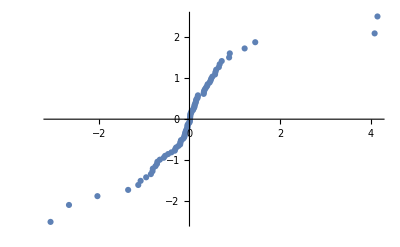

```mathematica
Block[{qObs,q0,labels,ix},
qObs=Flatten[midChi];
labels=Flatten[Table[measuredMetNames⟦i⟧,{i,Length[midChi]},{Length[midChi⟦i⟧]}]];
ix=Ordering[qObs];
q0=Quantile[NormalDistribution[0,1],N[(Range[Length[qObs]]-1/2)/Length[qObs]]];
ListPlot[
Thread[Tooltip[Transpose[{qObs⟦ix⟧,q0}],labels⟦ix⟧]],
PlotRange->All]]
```

Chi square = sum of squared residuals

```mathematica
TableForm[midChi^2,TableHeadings->{measuredMetNames,None}]
```

akg | 0.725976 | 0.229469 | 0.151708 | 0.0348182 | 0.0122963 | 0.0985771 | 
ala-L | 0.098529 | 0.667176 | 0.104362 | 0.0323512 |  |  | 
arg-L | 0.000333004 | 0.00170211 | 0.0120542 | 5.62806×10^-6 | 0.00767427 | 0.00192423 | 0.00221445
asp-L | 0.000453288 | 0.00600058 | 1.83387 | 2.10608 | 0.00166931 |  | 
cit | 4.1307 | 0.443924 | 0.131808 | 0.0222131 | 0.0164925 | 0.506256 | 0.00019889
citr-L | 0.291173 | 0.197356 | 0.000381096 | 0.0000444109 | 0.0996466 | 0.105733 | 0.00618876
glc-D | 17.2168 | 1.16424 | 9.40843 | 7.07741 | 0.914912 | 0.223662 | 16.7017
glc-D_EC | 0.21609 | 0.0425535 | 0.428157 | 0.0871796 | 0.00815975 | 0.00870257 | 0.765011
gln-L | 0.0200036 | 0.791336 | 0.563221 | 0.158832 | 0.254852 | 0.0108051 | 
glu-L | 0.00191225 | 1.48168 | 0.501121 | 0.655238 | 0.346612 | 0.0599691 | 
gly | 0.035145 | 0.000137285 | 0.0308891 |  |  |  | 
glyc3p | 0.00457295 | 0.419605 | 0.514632 | 0.0188328 |  |  | 
mal-L | 0.327444 | 0.0128459 | 1.27885 | 0.317959 | 0.0140615 |  | 
orn | 0.324036 | 0.115528 | 0.000267122 | 0.0000740271 | 0.160221 | 0.0383673 | 
ser-L | 0.0109602 | 0.0209238 | 0.00210265 | 0.0414068 |  |  |

```mathematica
Total[Flatten[midChi^2]]
```

74.8789

Flux errors

```mathematica
fluxChi=Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
v=Join[EMUFluxMap[net][fluxGams],BoundaryFlux[fluxGams]];
ix=ReindexList[measReactions,rl];
(fluxMixing.v⟦ix⟧-boundaryFluxMean)/boundaryFluxSD];
```

```mathematica
TableForm[fluxChi,TableHeadings->{measuredBoundaryIds,None}]
```

meas_ala-L | -0.0492176
meas_arg-L | 1.05988
meas_asp-L | -0.0136898
meas_cellwork | -3.19308
meas_glc-D | 0.118726
meas_glc-D_tot | -0.239522
meas_gln-L | 0.637244
meas_gly | -0.022786
meas_glycogen | -0.0237002
meas_lac-L | -0.0224273
meas_nadph_demand | 0.355417
meas_protdeg_ala | -0.107894
meas_protdeg_arg | -0.403993
meas_protdeg_asp | -0.0749418
meas_protdeg_glu | 0.985807
meas_protsyn_ala | -0.072553
meas_protsyn_arg | 1.33058
meas_protsyn_asp | -0.0764773
meas_protsyn_glu | -0.603849
meas_ser-L | -0.0114257
meas_urea | -1.82342

```mathematica
Total[Flatten[{midChi^2,fluxChi^2}]]
```

93.4295

### Flux confidence intervals

```mathematica
fluxCI=ImportGAMSFluxCI[gamsDir,gamsModelName,net];
```

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Dimensions[fluxCI]
```

{84,2}

Table of determined confidence intervals, taking the optimized reaction from each vector

```mathematica
fluxCIValues=Block[{ix},
ix=ReindexList[fluxCIReactions,Reactions[net]];
Table[
(NetFlux/@fluxCI⟦i⟧)⟦All,ix⟦i⟧⟧,
{i,Length[fluxCIReactions]}]];
```

```mathematica
TableForm[fluxCIValues,TableHeadings->{ReactionID/@fluxCIReactions,{" min"," max"}}]
```

|  min |  max
2AMACHYD | 0.001 | 649.894
ACONTm | 85.0128 | 411.668
ADK1 | 15.2338 | 108.632
AKGDm | 0.001 | 486.239
AKGtm | -39827.4 | 645.798
ALATA_L | -0.51815 | 57.1963
ALAtl | 20.67 | 58.0635
ARGN | 15.2338 | 108.632
ARGSL | 15.2338 | 108.632
ARGSS | 15.2338 | 108.632
ARGtl | 10.4296 | 15.1726
ASPTA | -110.089 | 42438.4
ASPTAm | 0.001 | 100000.
ASPtl | 10.7626 | 35.4095
ASPtm | 0.001 | 42516.7
ATPS4m | 314.486 | 6212.13
ATPtm | 204.821 | 6482.62
CBPSam | 0.001 | 120.297
CELLWORK | 0.001 | 6221.87
CO2tm | -1424.22 | 9319.42
CSm | 45.7677 | 411.668
CYOOm | 104.64 | 815.498
CYOR-u10m | 209.281 | 1631.
ENO | -794.313 | 827.284
FBA | 58.5345 | 394.343
FBP | 0.001 | 3081.13
FUMm | 0.002 | 693.756
FUMtm | 15.2338 | 121.637
G3PD1 | 0.0012125 | 641.456
G6PPer | 20.281 | 301.069
G6Pter | -212.292 | 27.1304
GAPD | -39.7073 | 518.395
GHMT2r | -18.5763 | 214.791
GLCmix | 890.617 | 1505.74
GLCtin | 3.49925 | 285.269
GLCtout | 18.927 | 301.069
GLNtm | 56.4918 | 67.7404
GLUDxm | -622.987 | 35.3752
GLUNm | 56.4918 | 67.7404
GLUtl | 21.3631 | 47.302
GLUt2m | -667.477 | 99593.3
GLYCOGEN_BREAK | 74.4408 | 325.527
GLYCPH | 0.0022125 | 1342.99
GLYK | 0.001 | 1175.1
GTHS | 0.001 | 222.06
H2Oter | 18.927 | 301.069
H2Otm | -4495.2 | -84.7879
HCO3Em | 145.055 | 2562.51
HEX1 | 4.42934 | 285.269
Htm2 | -3877.26 | 614.678
ICDHxm | 45.7677 | 521.878
LDH_L | 56.0534 | 86.8642
MALtm | -2444.97 | 33907.7
MDH | -62182.8 | 2444.97
MDHm | -1390.03 | 1156.51
NADH2-u10m | 0.001 | 2122.99
NADH_REDOX | -30806.8 | 2733.34
NDPK1 | 153.702 | 2548.4
NH4tm | 0.001 | 1022.18
O2tm | 104.64 | 815.498
OCBTm | 0.001 | 108.632
ORNt4m | 0.001 | 108.632
PCm | 49.0139 | 2473.42
PDHm | 85.0128 | 521.878
PEPCK | 153.702 | 2538.39
PFK | 58.5355 | 3262.58
PGCD | 0.00583822 | 1067.94
PGI | 58.5345 | 309.79
PGK | 27.9481 | 388.402
PGM | -726.281 | 827.284
PGMTer | 74.4408 | 410.04
PIt2m | 204.821 | 6482.62
PIter | -65.4236 | 288.402
PPA | 0.001 | 121.637
PROTDEG_ALA | 6.10198 | 68.5993
PROTDEG_ARG | 10.4296 | 15.1726
PROTDEG_ASP | 4.42443 | 43.8423
PROTDEG_GLU | 9.81494 | 40.1135
PROTSYN_ALA | 4.21818 | 67.5727
PROTSYN_ARG | 28.8947 | 38.7595
PROTSYN_ASP | 2.61119 | 43.4917
PROTSYN_GLU | 0.001 | 43.0214
PSERT | 0.00583822 | 1067.94
PSP_L | 0.00583823 | 662.271
PYK | 0.001 | 3272.37
PYRt2m | 264.044 | 3402.19
SERHL | 0.001 | 1022.18
SUCD1m | 0.001 | 486.239
SUCOASm | 0.001 | 486.239
TPI | -266.572 | 194.161

Plot intervals

```mathematica
fluxCIValues
```

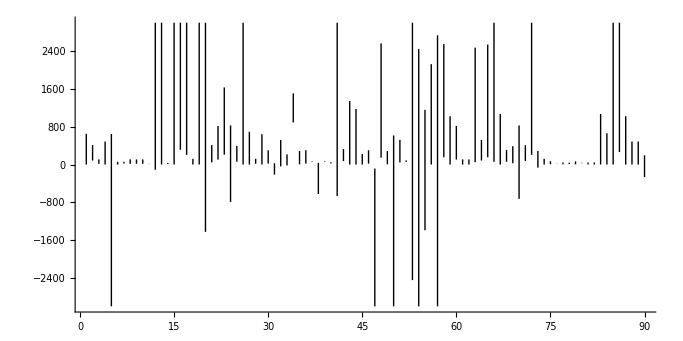

```mathematica
With[{fmax=3000},Graphics[
Table[
Line[{{i,Clip[fluxCIValues⟦i,1⟧,{-fmax,fmax}]},{i,Clip[fluxCIValues⟦i,2⟧,{-fmax,fmax}]}}],
{i,Length[fluxCIValues]}],
Axes->True,AspectRatio->1/2]]
```

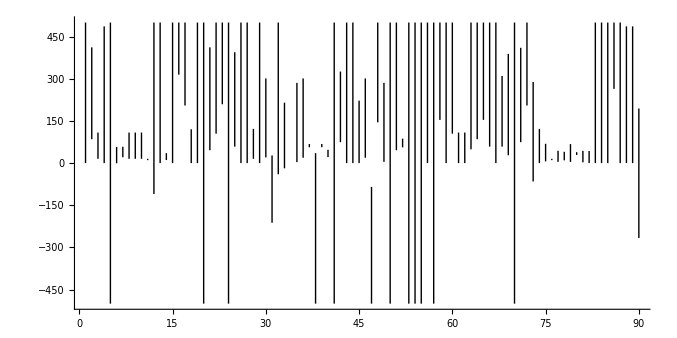

```mathematica
With[{fmax=500},Graphics[
Table[
Line[{{i,Clip[fluxCIValues⟦i,1⟧,{-fmax,fmax}]},{i,Clip[fluxCIValues⟦i,2⟧,{-fmax,fmax}]}}],
{i,Length[fluxCIValues]}],
Axes->True,AspectRatio->1/2]]
```

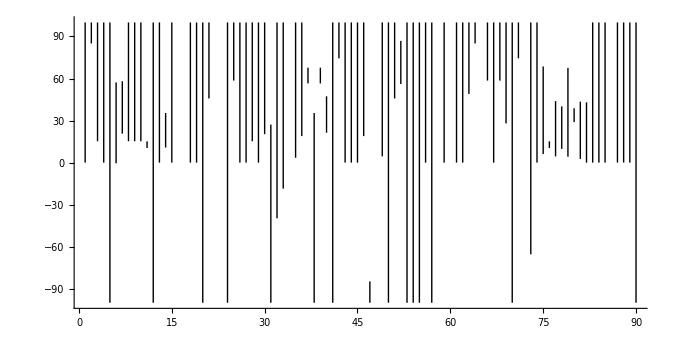

```mathematica
With[{fmax=100},Graphics[
Table[
Line[{{i,Clip[fluxCIValues⟦i,1⟧,{-fmax,fmax}]},{i,Clip[fluxCIValues⟦i,2⟧,{-fmax,fmax}]}}],
{i,Length[fluxCIValues]}],
Axes->True,AspectRatio->1/2]]
```

Flux vectors for specific optim

```mathematica
Position[fluxCIReactions,Reaction["G6Pter",__]]
```

{{31}}

```mathematica
Block[{i=31},
TableForm[
Transpose[NetFlux/@fluxCI⟦i⟧],
TableHeadings->{ReactionID/@Reactions[net],{"vmin","vmax"}}]]
```

| vmin | vmax
2AMACHYD | 513.581 | 466.935
ACONTm | 224.299 | 252.25
ADK1 | 91.4226 | 89.0955
AKGDm | 295.67 | 321.759
AKGtm | 472.929 | 293.102
ALATA_L | 28.865 | 28.0239
ALAtl | 38.455 | 36.9872
ARGN | 91.4226 | 89.0955
ARGSL | 91.4226 | 89.0955
ARGSS | 91.4226 | 89.0955
ARGtl | 12.6976 | 12.6935
ASPTA | 0. | 137.8
ASPTAm | 83.1317 | 216.487
ASPtl | 23.6646 | 25.493
ASPtm | 83.1317 | 216.487
ATPS4m | 1233.45 | 2118.18
ATPtm | 1095.24 | 2061.04
CBPSam | 91.4226 | 89.0955
CELLWORK | 354.586 | 1490.9
CO2tm | -401.813 | -536.461
CSm | 224.299 | 252.25
CYOOm | 305.823 | 487.987
CYOR-u10m | 611.647 | 975.974
ENO | -330.693 | -255.037
FBA | 305.252 | 138.886
FBP | 0.001 | 0.001
FUMm | 387.093 | 410.855
FUMtm | 91.4226 | 89.0955
G3PD1 | 439.404 | 73.8837
G6PPer | 108.682 | 181.94
G6Pter | -212.292 | 27.1304
GAPD | 171.1 | 203.889
GHMT2r | -8.29706 | -4.94605
GLCmix | 1155.6 | 1056.45
GLCtin | 92.9603 | 166.017
GLCtout | 108.682 | 181.94
GLNtm | 62.5308 | 62.24
GLUDxm | -484.689 | -440.079
GLUNm | 62.5308 | 62.24
GLUtl | 30.9743 | 29.2996
GLUt2m | -464.088 | -285.832
GLYCOGEN_BREAK | 320.974 | 154.809
GLYCPH | 439.405 | 109.784
GLYK | 0.001 | 35.9005
GTHS | 0.001 | 0.001
H2Oter | 108.682 | 181.94
H2Otm | -1313.41 | -2519.09
HCO3Em | 342.455 | 289.797
HEX1 | 92.9603 | 166.017
Htm2 | -885.661 | -1934.4
ICDHxm | 224.299 | 252.25
LDH_L | 67.1164 | 67.5904
MALtm | -330.694 | -142.82
MDH | 330.694 | 142.82
MDHm | 56.3983 | 268.035
NADH2-u10m | 315.977 | 654.215
NADH_REDOX | 497.068 | 664.16
NDPK1 | 330.694 | 280.62
NH4tm | 513.581 | 466.935
O2tm | 305.823 | 487.987
OCBTm | 91.4226 | 89.0955
ORNt4m | 91.4226 | 89.0955
PCm | 251.032 | 200.702
PDHm | 224.299 | 252.25
PEPCK | 330.694 | 280.62
PFK | 305.253 | 138.887
PGCD | 501.794 | 458.926
PGI | 305.252 | 138.886
PGK | 171.1 | 203.889
PGM | -330.693 | -255.037
PGMTer | 320.974 | 154.809
PIt2m | 1095.24 | 2061.04
PIter | 212.292 | -27.1304
PPA | 91.4226 | 89.0955
PROTDEG_ALA | 38.455 | 36.9872
PROTDEG_ARG | 12.6976 | 12.6935
PROTDEG_ASP | 23.6646 | 25.493
PROTDEG_GLU | 30.9743 | 29.2996
PROTSYN_ALA | 34.8889 | 34.2598
PROTSYN_ARG | 33.8343 | 33.8396
PROTSYN_ASP | 22.9355 | 22.639
PROTSYN_GLU | 22.1325 | 22.0289
PSERT | 501.794 | 458.926
PSP_L | 501.794 | 458.926
PYK | 0.001 | 25.583
PYRt2m | 475.33 | 452.951
SERHL | 513.581 | 466.935
SUCD1m | 295.67 | 321.759
SUCOASm | 295.67 | 321.759
TPI | -134.152 | 65.0027

HIghlighted network

```mathematica
Block[{i=31,fmax=1000},
GraphMLHighlightEdges[
FileNameJoin[{modelDir,"liver-model-2_openFluxExport.graphml"}],
ReactionID/@Reactions[net],Rescale[NetFlux[fluxCI⟦i,2⟧],{-fmax,fmax},{-10,10}],
FileNameJoin[{"L020","graphml","GLCtout-max.graphml"}]]]
```

L020\graphml\GLCtout-max.graphml

```mathematica
TableForm[
Transpose[Join@@Map[BoundaryFlux,fluxCI,{2}]],
TableHeadings->{
BoundaryFluxNames[bnet],
Join@@Outer[StringJoin,ReactionID/@fluxCIReactions,{" min"," max"}]}]
```

### Spot check simulated MIDs

Check specific MIDs

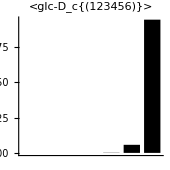
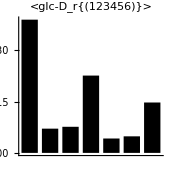
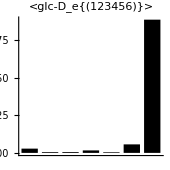
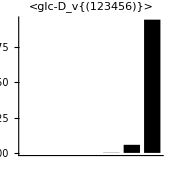

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["glc-D",_,_],{{{1,2,3,4,5,6}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

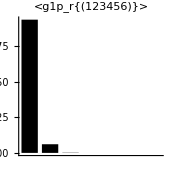
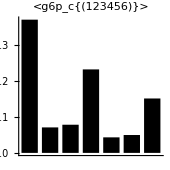
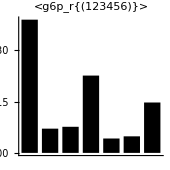

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g6p"|"g1p",_,_],{{{1,2,3,4,5,6}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

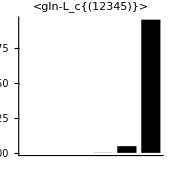
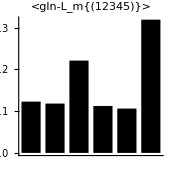

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["gln-L",_,_],{{{1,2,3,4,5}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

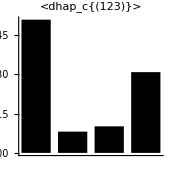
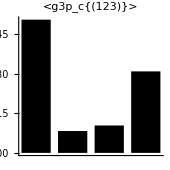
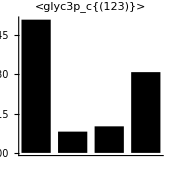

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g3p"|"dhap"|"glyc3p",__],{{{1,2,3}}}]]];
Table[ 
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

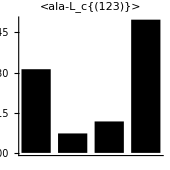
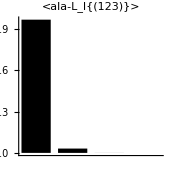
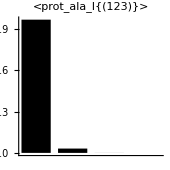
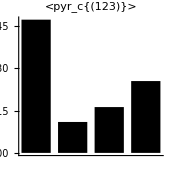
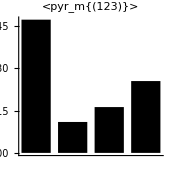

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["pyr"|"ala-L"|"prot_ala",_,_],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

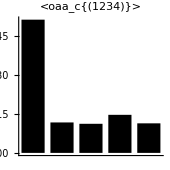
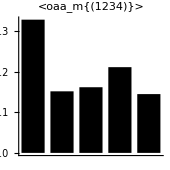

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["oaa",_,_],{{{1,2,3,4}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

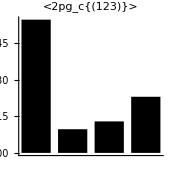
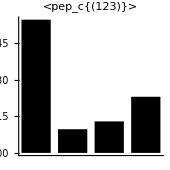

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["pep"|"2pg",_,_],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```